# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Assignment 08

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 1.

A lookback option is a path dependent option whose value is based on some function of the underlying’s price history over the life of the option/ rather than the price at expiry. Read the Wikipedia article https://en.wikipedia.org/wiki/Lookback_option which describes these options in detail.

There are many possible forms; however, the particular case for this assignment is a lookback put with:

P(T)=max[max_t [S(t)]-S(T),0]=S_max-S(T)

Assume a stock with price S(0)=$96.25 and volatility σ=28%, and a risk free rate r_f=0.5%. Use a Monte Carlo simulation to price the lookback option above for an expiry of T=0.75. Compare your solution to that returned by FinancialDerivative[ ].

Note: The corresponding Mathematica solution is identified as a {“LookbackFloating”, “European”, “Put”}. Use the Mathematica documentation to determine the required parameters for FinancialDerivative[ ].

### Solution

As with the case of the Asian option we need to generate sample paths that we can use to apply an appropriate function to. Let δ_Δ denote the random vector below:

δ_Δ=(r - σ^2/2)Δ + σ RandomVariate[NormalDistribution[0.,√Δ],T/Δ]

Let S(0,T|Δ) denote a random price path from t=0 to T in increments of Δ. Then

S(0,T|Δ)=S(0) Exp[FoldList[Plus,0,δ_Δ]]

We repeat this experiment M times with the j^th estimate being

P^(j)(T)=max[max[S(0,T|Δ)]-S(T),0]

and the risk neutral estimate of the option price being

P̂[0]=Exp[-r T]/J∑_(j=1)^M P_(j)(T)

#### Code

We only need a single line of code to compute the Monte Carlo estimate, including the simulation’s standard error. Whether you express your function as a single line or break it up into multiple lines depends upon both clarity and efficiency. For an experienced programmer figuring out the logic of the code below would not be difficult, but there is no problem breaking it into separate steps if you find that clearer or more maintainable. Here’s a rather coarse path using Δ=0.1 as an illustration. Note that The number of steps is T/Δ=1/0.1, and we would want to insure that this is an integer.

```mathematica
95. Exp[FoldList[Plus,0.,(0.02-0.10^2/2.)0.1+0.10 RandomVariate[NormalDistribution[0.,√0.1],1./0.1]]]
```

{95.,96.4224,95.3743,96.1576,97.8991,94.2734,96.8544,99.4851,95.2379,101.687,95.8486}

In terms of the variables described above we define a function

xAsianLookbackPutMonteCarlo[S(0),σ,r,T,Δ,M]

```mathematica
xLookbackFloatingPutMonteCarlo[nInitialPrice_,nVolatility_,nRiskFree_,nExpiry_,nDeltaT_,iNSamples_]:=
{Mean[#],StandardDeviation[#]/√iNSamples}&[
Exp[-nRiskFree nExpiry]
Table[
(Max[#]-Last[#]&)[nInitialPrice Exp[FoldList[Plus,0.,(nRiskFree-nVolatility^2/2.)nDeltaT+nVolatility RandomVariate[NormalDistribution[0.,√nDeltaT],nExpiry/nDeltaT]]]],
{iNSamples}
]
]
```

```mathematica
xLookbackFloatingPutMonteCarlo[96.25,0.28,0.005,0.75,0.75/100,1000]
```

{18.0805,0.397604}

The simulation study below returns a vector of points representing the underlying price at various levels vs. the lower 95% confidence limit, mean, and upper 95% confidence limit for the option price. The vector of such results is then transposed to yield three lines representing the lower confidence level, mean, and upper confidence level.

```mathematica
mnSim=Transpose@Block[
{sol},
Table[
sol=xAsianArithPutMonteCarlo[price,0.1,100.,1.,0.0005,0.02,1./0.0005,1000.];
{{price,sol⟦1⟧-1.96sol⟦2⟧},{price,sol⟦1⟧},{price,sol⟦1⟧+1.96sol⟦2⟧}},
{price,80.,120.,5.}
]
]
```

{{{80.,79.804},{85.,84.804},{90.,89.804},{95.,94.804},{100.,99.804},{105.,104.804},{110.,109.804},{115.,114.804},{120.,119.804}},{{80.,80.},{85.,85.},{90.,90.},{95.,95.},{100.,100.},{105.,105.},{110.,110.},{115.,115.},{120.,120.}},{{80.,80.196},{85.,85.196},{90.,90.196},{95.,95.196},{100.,100.196},{105.,105.196},{110.,110.196},{115.,115.196},{120.,120.196}}}

A comparison of our solutions and those of Mathematica’s FinancialDerivative[ ] follows.

```mathematica
mnSim[[2]]
```

{{80.,80.},{85.,85.},{90.,90.},{95.,95.},{100.,100.},{105.,105.},{110.,110.},{115.,115.},{120.,120.}}

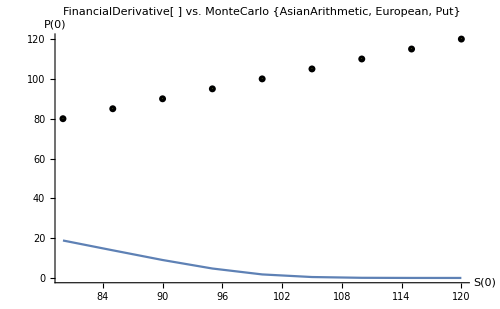

```mathematica
Show[
ListLinePlot[Table[{price,FinancialDerivative[{"AsianArithmetic","European","Put"},{"StrikePrice"->100.,"Expiration"->1.,"Inception"->0.,"AverageSoFar"->95.},
{"CurrentPrice"->price,"Volatility"->0.10,"InterestRate"->0.02}]},{price,80,120,5}],PlotLabel->Style["FinancialDerivative[ ] vs. MonteCarlo\n{AsianArithmetic, European, Put}",FontSize->16],AxesLabel->(Style[#,FontSize->14]&/@{"S(0)","P(0)"})],
ListPlot[mnSim,PlotStyle->{{PointSize[0]},{Black,PointSize[0.01]},{PointSize[0]}},Filling->{1->{3}},FillingStyle->Red],PlotRange->All,ImageSize->500
]
```

Again, note that the Mathematica function itself uses Monte Carlo. It returns a slightly different result each time it is run. We’ll sample it to see how much it varies from call to call.

```mathematica
vnMmaSim=Table[FinancialDerivative[{"AsianArithmetic","European","Put"},{"StrikePrice"->100.,"Expiration"->1.,"Inception"->0.,"AverageSoFar"->95.},
{"CurrentPrice"->95.,"Volatility"->0.10,"InterestRate"->0.02}],{100}];
```

Note in the histogram below we have plotted the standard deviation of the simulated results, not the standard error of the mean.

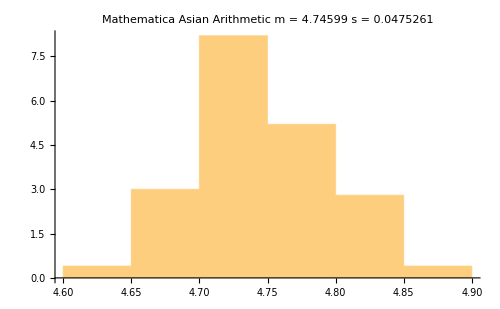

```mathematica
Histogram[vnMmaSim,Automatic,"PDF",PlotLabel->Style["Mathematica Asian Arithmetic\n m = "<>ToString[Mean[vnMmaSim]]<>" s = "<>ToString[StandardDeviation[vnMmaSim]],FontSize->16],ImageSize->500]
```